```mathematica
Clear["Global`*"]
```

# Bulmer's (1989) model on Fisherian sexual selection

## Define genotypes and basic functions

```mathematica
allelesT={T1,T2};
allelesP={P1,P2};
```

Define each genotype and describe its frequency in terms of the underlying allele frequencies (t1, p1, t2, p2) and the linkage disequilibria (see Rice 2004, p.45)

```mathematica
genotypes={{T1,P1},{T1,P2},{T2,P1},{T2,P2}};
alleleFreqsLD={t1 p1+𝒟,t1 p2-𝒟,t2 p1-𝒟,t2 p2+𝒟};
```

Function to translate the genotype-based mating probabilities back to allele-based mating probabilities as in the AREES paper, Rice 2004 and Bulmer 1989 (see below)

```mathematica
Υ[i_,j_]:=U[If[i==1||i==3,1,2],If[j==1||j==2,1,2]]
```

## Contributions of matings to each haplotype

As opposed to what Sean Rice is doing (he numbers by x11, x12, x21, x22), I number genotype frequencies like x_1,x_2,x_3,x_4. Based on these indices 1,2,3,4 I can then make a function which calculates the probability that mom with genotype number momGenoId mates with a dad having genotype number dadGenoId, resulting in an offspring with genotype number offGenoId:

```mathematica
matingtable[momGenoId_,dadGenoId_,offGenoId_]:=Module[{matingProb,genoMom,genoDad,genoOff,genoNonRecomb,genoRecomb},
(* calculate the mating probability, which is the product of the female genotype frequency x[i] times the proportion of surviving males with a certain ornament xs[j]/ts[k] times the mating probability Υ[i,j] *)
matingProb=x[momGenoId] x[dadGenoId]/If[dadGenoId≥3,t2,t1] Υ[momGenoId,dadGenoId];
(* get the actual genotypes of mom, dad and offspring *)
genoMom=genotypes[[momGenoId]];
genoDad=genotypes[[dadGenoId]];
genoOff=genotypes[[offGenoId]];
(* get a list of all genotypes produced without recombination *)
genoNonRecomb={genoMom,genoDad};
(* get a list of all genotypes produced with recombination *)
genoRecomb={{genoMom[[1]],genoDad[[2]]},{genoDad[[1]],genoMom[[2]]}};
(* Count how many occurrences of the desired offspring genotype occur in all possible genotypes from this pair *)
Return[Simplify[matingProb*((1-r)Count[genoNonRecomb,genoOff]/2+r Count[genoRecomb,genoOff]/2)]]
]
```

Test with examples (see table in Rice's 2004 book p. 61), such as T_1 P_1 x T_2 P_2 yielding offspring with genotype T_2 P_2:

```mathematica
matingtable[1,4,4]//Simplify
```

-((-1+r) U[1,2] x[1] x[4])/(2 t2)

Note that the function above considers that the proportion of males with genotype T_k P_m out of all males who bear the ornament allele T_k is given by x_km'/t_k' (primes denoting frequencies 	after natural selection). However, all males bearing a particular ornament allele have the same survival, so we can write x_km'/t_k'=x_km/t_k.

### Genotype frequencies in the next generation

Calculate the frequency x_k of genotype k in the next generation by summing over all possible parental matings and calculating the probabilities that offspring with genotype k are produced

```mathematica
xtplus1[k_]:=Sum[matingtable[i,j,k],{i,1,4},{j,1,4}];
```

## Frequencies of t_2, p_2 and linkage disequilibrium 𝒟 in the next generation

Function to substitute a genotype frequency x_i for the corresponding product of allele frequencies plus the gametic disequilibrium

```mathematica
𝓍[i_]:=alleleFreqsLD[[i]]
```

Check whether total change of all genotype frequencies sums to one, as should be the case when females bear no costly preference:

```mathematica
xtplus1[1]+xtplus1[2]+xtplus1[3]+xtplus1[4]//Simplify
```

((x[1]+x[2]) (U[1,1] (x[1]+x[3])+U[2,1] (x[2]+x[4])))/t1+((x[3]+x[4]) (U[1,2] (x[1]+x[3])+U[2,2] (x[2]+x[4])))/t2

Making some handy substitutions, we indeed obtain:

```mathematica
xtplus1[1]+xtplus1[2]+xtplus1[3]+xtplus1[4]/.{y[1]->(1-tm)-y[2],y[3]->tm-y[4]}/.x->𝓍/.{U[1,1]->1-U[1,2],U[2,1]->1-U[2,2]}/.{p1->1-p2,t1->1-t2}/.{U[1,2]->tm,U[2,2]-> a tm/(1-tm+a tm)}/.tm->t2/(1-s t2)//Expand//Simplify
```

1

### Frequency change of t2

To calculate allele frequency change, substitute genotype frequencies for their productions of allele frequencies + linkage disequilibria. Then use the fact that Ui1+Ui2=1 and make further simplifications, yielding:

```mathematica
t2tplus1=xtplus1[3]+xtplus1[4]/.x->𝓍/.{U[1,1]->1-U[1,2],U[2,1]->1-U[2,2]}/.{p1->1-p2,t1->1-t2}//Simplify
```

1/2 (t2-(-1+p2) U[1,2]+p2 U[2,2])

```mathematica
Δt2=t2tplus1-t2//Simplify
```

1/2 (-t2-(-1+p2) U[1,2]+p2 U[2,2])

... which is eq. 2.27 from Rice 2004 and when adding t2 we obtain the difference equation (expression 1a in Bulmer 1989 TPB). From this, we can obtain the expression A1 from Kuijper et al 2012 by doing the following: first of all note that I use here U_12 rather than U_10 to facilitate indexing in Mathematica. Clubbing the p_2s in the expression above and rewriting the remaining U_12=t_m, as the probability that an ornament male is chosen by a randomly mating female is equal to its frequency after survival (here written as tm) so that we obtain

```mathematica
A1AREES=1/2(p2 (U[2,2]-U[1,2])-(t2-tm));
```

### Frequency of p1 in the next generation

```mathematica
p2tplus1=xtplus1[2]+xtplus1[4]/.x->𝓍/.{U[1,1]->1-U[1,2],U[2,1]->1-U[2,2]}/.{p1->1-p2,t1->1-t2}//Simplify
```

(2 p2 t2-2 p2 t2^2-t2 𝒟+𝒟 U[1,2]-p2 𝒟 U[1,2]+p2 𝒟 U[2,2])/(2 t2-2 t2^2)

```mathematica
Δp2=p2tplus1-p2/.x->𝓍/.{U[1,1]->1-U[1,2],U[2,1]->1-U[2,2]}/.{p1->1-p2,t1->1-t2}//Simplify
```

(𝒟 (t2+(-1+p2) U[1,2]-p2 U[2,2]))/(2 (-1+t2) t2)

Which is eq. 2.28 in Rice (2004). We can obtain the expression in the AREES supplement again in the same way as noted for Δt_2 above.

### Frequency change of linkage disequilibrium D

We calculate Δ𝒟=x_(4,t+1)-t_(2,t+1)p_(2,t+1)-𝒟_t:

```mathematica
Δ𝒟=xtplus1[4]-p2tplus1 t2tplus1-𝒟/.x->𝓍/.{U[1,1]->1-U[1,2],U[2,1]->1-U[2,2]}/.{p1->1-p2,t1->1-t2}//Simplify
```

1/(4 (-1+t2) t2)(t2^2 (-3 𝒟+2 (-1+p2) p2 r (U[1,2]-U[2,2]))+2 t2 (-(-1+p2) p2 r (U[1,2]-U[2,2])+𝒟 (1+r-(-1+p2) U[1,2]+2 (-1+p2) r U[1,2]+p2 U[2,2]-2 p2 r U[2,2]))+𝒟 ((-1+p2)^2 U[1,2]^2+U[2,2] (2 p2 (-1+r)-2 r 𝒟+p2^2 U[2,2])+2 U[1,2] (-1+r+r 𝒟-p2^2 U[2,2]+p2 (1-r+U[2,2]))))

Linkage disequilibria are nearly always a complicated story. However, let's see if we can get some insight by clubbing powers of 𝒟. Clubbing in powers of 𝒟 always helps, also to see whether approximating things in terms of weak 𝒟 will have an effect. No approximations necessary here, however:

```mathematica
dcoeff=CoefficientList[Δ𝒟,𝒟]//Simplify
```

{1/2 (-1+p2) p2 r (U[1,2]-U[2,2]),1/(4 (-1+t2) t2)(-3 t2^2+((-1+p2) U[1,2]-p2 U[2,2]) (2-2 r+(-1+p2) U[1,2]-p2 U[2,2])+2 t2 (1+r-(-1+p2) U[1,2]+2 (-1+p2) r U[1,2]+p2 U[2,2]-2 p2 r U[2,2])),(r (U[1,2]-U[2,2]))/(2 (-1+t2) t2)}

We can see that first and third terms immediately yield the last part in A2:

```mathematica
A2lastpart=dcoeff[[1]]+𝒟^2 dcoeff[[3]]//Expand//FullSimplify
```

(r ((-1+p2) p2 (-1+t2) t2+𝒟^2) (U[1,2]-U[2,2]))/(2 (-1+t2) t2)

which becomes even clearer when we write U[2,2] in terms of B, as defined in eq A2

```mathematica
U22subB={U[2,2]->B t2(1-t2)+U[1,2]};
```

and substituting

```mathematica
A2lastpart=A2lastpart/.U22subB//FullSimplify
```

1/2 B r ((-1+p2) p2 (-1+t2) t2+𝒟^2)

Leaving the second term in dcoeff. Separating parts with and without recombination, we have

```mathematica
dcoeff2=CoefficientList[dcoeff[[2]],r]//Expand//FullSimplify
```

{-((t2+(-1+p2) U[1,2]-p2 U[2,2]) (-2+3 t2-(-1+p2) U[1,2]+p2 U[2,2]))/(4 (-1+t2) t2),(t2-(-1+p2) U[1,2]+2 (-1+p2) t2 U[1,2]+p2 U[2,2]-2 p2 t2 U[2,2])/(2 (-1+t2) t2)}

Can we further simplify this? Well, we can substitute in for the expression of A as in the AREES paper. Here I do so by rewriting U[2,2] in terms of A

```mathematica
U22subA={U[2,2]->(t2 (1+A-A t2)+(-1+p2) U[1,2])/p2}
```

{U[2,2]→(t2 (1+A-A t2)+(-1+p2) U[1,2])/p2}

Substituting for U22 we then obtain the first part of expression A1

```mathematica
A2firstpart=𝒟(dcoeff2[[1]]+dcoeff2[[2]]r)/.U22subA//Simplify
```

1/4 (-4 r+A^2 (-1+t2) t2+2 A (-1+r) (-1+2 t2)) 𝒟

So that we have

```mathematica
A2firstpart+A2lastpart//Simplify
```

1/4 ((-4 r+A^2 (-1+t2) t2+2 A (-1+r) (-1+2 t2)) 𝒟+2 B r ((-1+p2) p2 (-1+t2) t2+𝒟^2))

## Numerically iterating the model

Specify the preference functions of the Kirkpatrick model (eqns. 2.30 in Rice 1994)

```mathematica
prefFuncKP={U[1,1]->t1m,U[1,2]->t2m,U[2,1]->t1m/(t1m+α t2m),U[2,2]->α t2m/(t1m+α t2m)}/.{t1m->(1-t2)/(1-s t2),t2m->t2(1-s)/(1-s t2)}//Simplify
```

{U[1,1]→(-1+t2)/(-1+s t2),U[1,2]→((-1+s) t2)/(-1+s t2),U[2,1]→(-1+t2)/(-1+t2+(-1+s) t2 α),U[2,2]→((-1+s) t2 α)/(-1+t2+(-1+s) t2 α)}

```mathematica
(* prefFuncSeger={U[1,1]->*)
```

Here, I make a function (Module[]) to numerically iterate the system of recursions for p2, t2 and D:

```mathematica
anyrandomTable=ConstantArray[0,{10,2}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
anyrandomTable//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
anyrandomTable[[{5,6},All]]=5
```

5

```mathematica
anyrandomTable//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0
5 | 5
5 | 5
0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
For[myIter=1,myIter≤5,myIter++,
Print[anyrandomTable[[myIter,All]]]
]
```

{0,0}

{0,0}

{0,0}

«1 more identical outputs»

{5,5}

```mathematica
numericallyIterate[𝓇_,𝓈_,𝒶_,preffunc_,p20_,t20_,D0_,tend_]:=Module[
(* specify local variables, i.e., those only used within the function *)
{Data,iter,valuesPreviousTimestep,subslist,nextTimeStep},

(* allocate space for a 0-filled dataset to store all the 
output from the iteration for three 
traits (p2, t2, D) for tend timesteps *)
Data=ConstantArray[0,{tend,3}];

(* make a list to easily substitute parameters *)
subslist={r->𝓇,s->𝓈,α->𝒶};

(* set the starting values for the first iteration,
after which these values evolve *)
Data[[1,All]]={p20,t20,D0};

(* now iterate t2tplus1 = ..., p2tplus1 = ..., 𝒟tplus1 = .... 
using a for-loop *)
For[iter=2,iter≤tend,iter++,

(* remember the values of p2, t2, 𝒟 from 
time t *)
valuesPreviousTimestep={p2->Data[[iter-1,1]],t2->Data[[iter-1,2]],𝒟->Data[[iter-1,3]]};

(* and use those to calculate the 
values for time t+1 *)
nextTimeStep={p2tplus1,t2tplus1,𝒟+Δ𝒟}/.preffunc/.valuesPreviousTimestep/.subslist;

(* restrict values between 0 and 1 *)
nextTimeStep=Clip[#,{0,1.0}]&/@nextTimeStep;

Data[[iter,All]]=nextTimeStep;
];
Return[Data]
]
```

```mathematica
testrun=numericallyIterate[0.4,0.1,1.2,prefFuncKP,0.08,0.1,0.1,300]
```

{{0.08,0.1,0.1},{0.075671,0.0961039,0.0585049},{0.0731166,0.0923111,0.0341979},{0.0716162,0.0886351,0.0200262},{0.0707353,0.0850816,0.0117859},{0.0702161,0.0816525,0.00700078},{0.0699075,0.078347,0.00422282},{0.0697213,0.0751631,0.00260883},{0.0696063,0.072098,0.00166911},{0.0695327,0.0691484,0.00111976},{0.0694833,0.0663111,0.000796375},{0.0694482,0.0635824,0.000603793},{0.0694216,0.060959,0.000486987},{0.0694002,0.0584374,0.00041414},{0.0693819,0.0560142,0.000366863},{0.0693658,0.053686,0.000334529},{0.0693511,0.0514496,0.000310997},{0.0693374,0.0493018,0.000292717},{0.0693245,0.0472394,0.000277635},{0.0693123,0.0452594,0.000264563},{0.0693006,0.0433589,0.000252809},{0.0692895,0.0415348,0.000241972},{0.0692789,0.0397845,0.000231813},{0.0692687,0.0381052,0.000222193},{0.0692589,0.0364942,0.000213024},{0.0692496,0.034949,0.000204254},{0.0692406,0.033467,0.000195848},{0.069232,0.032046,0.000187779},{0.0692237,0.0306834,0.00018003},{0.0692158,0.0293772,0.000172587},{0.0692083,0.028125,0.000165436},{0.069201,0.0269248,0.000158566},{0.069194,0.0257745,0.000151967},{0.0691874,0.0246722,0.000145629},{0.069181,0.023616,0.000139542},{0.0691748,0.022604,0.000133698},{0.069169,0.0216344,0.000128088},{0.0691634,0.0207056,0.000122704},{0.069158,0.019816,0.000117536},{0.0691528,0.0189638,0.000112578},{0.0691479,0.0181477,0.000107821},{0.0691431,0.0173661,0.000103258},{0.0691386,0.0166176,0.0000988819},{0.0691343,0.0159009,0.000094685},{0.0691301,0.0152146,0.0000906607},{0.0691261,0.0145576,0.0000868025},{0.0691223,0.0139285,0.0000831038},{0.0691187,0.0133263,0.0000795584},{0.0691152,0.0127498,0.0000761605},{0.0691119,0.012198,0.0000729041},{0.0691087,0.0116697,0.0000697837},{0.0691056,0.0111641,0.0000667939},{0.0691027,0.0106802,0.0000639294},{0.0690999,0.0102171,0.0000611853},{0.0690972,0.00977382,0.0000585567},{0.0690946,0.00934963,0.0000560389},{0.0690922,0.00894369,0.0000536275},{0.0690898,0.00855524,0.000051318},{0.0690876,0.00818352,0.0000491064},{0.0690854,0.00782784,0.0000469887},{0.0690834,0.0074875,0.0000449609},{0.0690814,0.00716187,0.0000430194},{0.0690795,0.0068503,0.0000411606},{0.0690777,0.0065522,0.000039381},{0.069076,0.006267,0.0000376775},{0.0690743,0.00599414,0.0000360468},{0.0690728,0.00573309,0.0000344859},{0.0690712,0.00548336,0.0000329918},{0.0690698,0.00524445,0.0000315618},{0.0690684,0.0050159,0.0000301932},{0.0690671,0.00479726,0.0000288833},{0.0690658,0.00458811,0.0000276298},{0.0690646,0.00438805,0.0000264302},{0.0690635,0.00419667,0.0000252823},{0.0690624,0.00401361,0.0000241838},{0.0690613,0.0038385,0.0000231327},{0.0690603,0.00367101,0.000022127},{0.0690593,0.0035108,0.0000211647},{0.0690584,0.00335756,0.0000202439},{0.0690575,0.00321099,0.000019363},{0.0690566,0.0030708,0.0000185202},{0.0690558,0.00293671,0.0000177138},{0.0690551,0.00280846,0.0000169424},{0.0690543,0.0026858,0.0000162044},{0.0690536,0.00256848,0.0000154984},{0.0690529,0.00245628,0.000014823},{0.0690523,0.00234896,0.0000141769},{0.0690517,0.00224633,0.0000135588},{0.0690511,0.00214817,0.0000129675},{0.0690505,0.00205429,0.000012402},{0.06905,0.00196451,0.000011861},{0.0690494,0.00187864,0.0000113435},{0.0690489,0.00179652,0.0000108486},{0.0690485,0.00171798,0.0000103751},{0.069048,0.00164287,9.92226×10^-6},{0.0690476,0.00157105,9.48911×10^-6},{0.0690472,0.00150235,9.07482×10^-6},{0.0690468,0.00143666,8.67856×10^-6},{0.0690464,0.00137383,8.29956×10^-6},{0.069046,0.00131375,7.93707×10^-6},{0.0690457,0.0012563,7.59037×10^-6},{0.0690453,0.00120135,7.25879×10^-6},{0.069045,0.0011488,6.94165×10^-6},{0.0690447,0.00109855,6.63835×10^-6},{0.0690444,0.0010505,6.34826×10^-6},{0.0690441,0.00100454,6.07083×10^-6},{0.0690439,0.000960599,5.8055×10^-6},{0.0690436,0.000918574,5.55175×10^-6},{0.0690434,0.000878386,5.30907×10^-6},{0.0690432,0.000839955,5.07698×10^-6},{0.0690429,0.000803204,4.85502×10^-6},{0.0690427,0.00076806,4.64275×10^-6},{0.0690425,0.000734453,4.43975×10^-6},{0.0690423,0.000702315,4.24561×10^-6},{0.0690421,0.000671582,4.05995×10^-6},{0.069042,0.000642194,3.8824×10^-6},{0.0690418,0.000614091,3.7126×10^-6},{0.0690416,0.000587217,3.55022×10^-6},{0.0690415,0.000561518,3.39494×10^-6},{0.0690413,0.000536943,3.24644×10^-6},{0.0690412,0.000513444,3.10443×10^-6},{0.069041,0.000490972,2.96863×10^-6},{0.0690409,0.000469484,2.83876×10^-6},{0.0690408,0.000448935,2.71457×10^-6},{0.0690407,0.000429286,2.5958×10^-6},{0.0690406,0.000410496,2.48223×10^-6},{0.0690404,0.000392529,2.37362×10^-6},{0.0690403,0.000375347,2.26977×10^-6},{0.0690402,0.000358918,2.17045×10^-6},{0.0690401,0.000343207,2.07548×10^-6},{0.0690401,0.000328184,1.98466×10^-6},{0.06904,0.000313818,1.89781×10^-6},{0.0690399,0.000300081,1.81476×10^-6},{0.0690398,0.000286945,1.73534×10^-6},{0.0690397,0.000274384,1.65939×10^-6},{0.0690397,0.000262373,1.58677×10^-6},{0.0690396,0.000250887,1.51733×10^-6},{0.0690395,0.000239904,1.45092×10^-6},{0.0690395,0.000229402,1.38742×10^-6},{0.0690394,0.000219359,1.32669×10^-6},{0.0690393,0.000209756,1.26862×10^-6},{0.0690393,0.000200573,1.2131×10^-6},{0.0690392,0.000191792,1.16×10^-6},{0.0690392,0.000183396,1.10922×10^-6},{0.0690391,0.000175367,1.06067×10^-6},{0.0690391,0.000167689,1.01424×10^-6},{0.069039,0.000160348,9.69847×10^-7},{0.069039,0.000153328,9.27393×10^-7},{0.069039,0.000146615,8.86797×10^-7},{0.0690389,0.000140196,8.47978×10^-7},{0.0690389,0.000134058,8.10857×10^-7},{0.0690388,0.000128189,7.75361×10^-7},{0.0690388,0.000122577,7.41419×10^-7},{0.0690388,0.00011721,7.08962×10^-7},{0.0690388,0.000112078,6.77926×10^-7},{0.0690387,0.000107171,6.48248×10^-7},{0.0690387,0.000102479,6.19869×10^-7},{0.0690387,0.0000979923,5.92732×10^-7},{0.0690386,0.000093702,5.66783×10^-7},{0.0690386,0.0000895994,5.4197×10^-7},{0.0690386,0.0000856765,5.18243×10^-7},{0.0690386,0.0000819253,4.95554×10^-7},{0.0690385,0.0000783383,4.73859×10^-7},{0.0690385,0.0000749084,4.53113×10^-7},{0.0690385,0.0000716286,4.33276×10^-7},{0.0690385,0.0000684925,4.14307×10^-7},{0.0690385,0.0000654936,3.96168×10^-7},{0.0690385,0.000062626,3.78823×10^-7},{0.0690384,0.000059884,3.62238×10^-7},{0.0690384,0.000057262,3.46378×10^-7},{0.0690384,0.0000547549,3.31213×10^-7},{0.0690384,0.0000523574,3.16712×10^-7},{0.0690384,0.000050065,3.02845×10^-7},{0.0690384,0.0000478729,2.89586×10^-7},{0.0690383,0.0000457768,2.76907×10^-7},{0.0690383,0.0000437725,2.64783×10^-7},{0.0690383,0.0000418559,2.5319×10^-7},{0.0690383,0.0000400233,2.42105×10^-7},{0.0690383,0.0000382708,2.31505×10^-7},{0.0690383,0.0000365952,2.21369×10^-7},{0.0690383,0.0000349928,2.11676×10^-7},{0.0690383,0.0000334607,2.02408×10^-7},{0.0690383,0.0000319956,1.93546×10^-7},{0.0690383,0.0000305946,1.85072×10^-7},{0.0690382,0.000029255,1.76969×10^-7},{0.0690382,0.0000279741,1.6922×10^-7},{0.0690382,0.0000267492,1.61811×10^-7},{0.0690382,0.000025578,1.54726×10^-7},{0.0690382,0.0000244581,1.47952×10^-7},{0.0690382,0.0000233872,1.41474×10^-7},{0.0690382,0.0000223631,1.35279×10^-7},{0.0690382,0.0000213839,1.29356×10^-7},{0.0690382,0.0000204476,1.23692×10^-7},{0.0690382,0.0000195523,1.18276×10^-7},{0.0690382,0.0000186962,1.13098×10^-7},{0.0690382,0.0000178776,1.08146×10^-7},{0.0690382,0.0000170948,1.03411×10^-7},{0.0690382,0.0000163463,9.88827×10^-8},{0.0690382,0.0000156305,9.45531×10^-8},{0.0690382,0.0000149461,9.0413×10^-8},{0.0690382,0.0000142917,8.64543×10^-8},{0.0690382,0.0000136659,8.26688×10^-8},{0.0690382,0.0000130676,7.90491×10^-8},{0.0690381,0.0000124954,7.55879×10^-8},{0.0690381,0.0000119483,7.22783×10^-8},{0.0690381,0.0000114251,6.91135×10^-8},{0.0690381,0.0000109248,6.60873×10^-8},{0.0690381,0.0000104465,6.31937×10^-8},{0.0690381,9.98906×10^-6,6.04267×10^-8},{0.0690381,9.55168×10^-6,5.77809×10^-8},{0.0690381,9.13345×10^-6,5.52509×10^-8},{0.0690381,8.73353×10^-6,5.28317×10^-8},{0.0690381,8.35112×10^-6,5.05184×10^-8},{0.0690381,7.98546×10^-6,4.83064×10^-8},{0.0690381,7.6358×10^-6,4.61913×10^-8},{0.0690381,7.30146×10^-6,4.41687×10^-8},{0.0690381,6.98176×10^-6,4.22348×10^-8},{0.0690381,6.67605×10^-6,4.03855×10^-8},{0.0690381,6.38373×10^-6,3.86171×10^-8},{0.0690381,6.10421×10^-6,3.69263×10^-8},{0.0690381,5.83693×10^-6,3.53094×10^-8},{0.0690381,5.58135×10^-6,3.37633×10^-8},{0.0690381,5.33697×10^-6,3.2285×10^-8},{0.0690381,5.10328×10^-6,3.08713×10^-8},{0.0690381,4.87983×10^-6,2.95196×10^-8},{0.0690381,4.66616×10^-6,2.8227×10^-8},{0.0690381,4.46184×10^-6,2.69911×10^-8},{0.0690381,4.26647×10^-6,2.58093×10^-8},{0.0690381,4.07966×10^-6,2.46792×10^-8},{0.0690381,3.90103×10^-6,2.35986×10^-8},{0.0690381,3.73021×10^-6,2.25653×10^-8},{0.0690381,3.56688×10^-6,2.15772×10^-8},{0.0690381,3.4107×10^-6,2.06324×10^-8},{0.0690381,3.26136×10^-6,1.9729×10^-8},{0.0690381,3.11855×10^-6,1.88652×10^-8},{0.0690381,2.982×10^-6,1.80391×10^-8},{0.0690381,2.85143×10^-6,1.72492×10^-8},{0.0690381,2.72658×10^-6,1.6494×10^-8},{0.0690381,2.60719×10^-6,1.57718×10^-8},{0.0690381,2.49303×10^-6,1.50812×10^-8},{0.0690381,2.38387×10^-6,1.44208×10^-8},{0.0690381,2.27949×10^-6,1.37894×10^-8},{0.0690381,2.17968×10^-6,1.31856×10^-8},{0.0690381,2.08424×10^-6,1.26082×10^-8},{0.0690381,1.99298×10^-6,1.20562×10^-8},{0.0690381,1.90571×10^-6,1.15283×10^-8},{0.0690381,1.82227×10^-6,1.10235×10^-8},{0.0690381,1.74248×10^-6,1.05408×10^-8},{0.0690381,1.66618×10^-6,1.00793×10^-8},{0.0690381,1.59322×10^-6,9.63794×10^-9},{0.0690381,1.52346×10^-6,9.21593×10^-9},{0.0690381,1.45675×10^-6,8.81239×10^-9},{0.0690381,1.39297×10^-6,8.42653×10^-9},{0.0690381,1.33197×10^-6,8.05756×10^-9},{0.0690381,1.27365×10^-6,7.70475×10^-9},{0.0690381,1.21788×10^-6,7.36739×10^-9},{0.0690381,1.16456×10^-6,7.04479×10^-9},{0.0690381,1.11356×10^-6,6.73633×10^-9},{0.0690381,1.06481×10^-6,6.44137×10^-9},{0.0690381,1.01818×10^-6,6.15932×10^-9},{0.0690381,9.73599×10^-7,5.88963×10^-9},{0.0690381,9.30968×10^-7,5.63174×10^-9},{0.0690381,8.90204×10^-7,5.38515×10^-9},{0.0690381,8.51225×10^-7,5.14935×10^-9},{0.0690381,8.13953×10^-7,4.92388×10^-9},{0.0690381,7.78313×10^-7,4.70828×10^-9},{0.0690381,7.44233×10^-7,4.50212×10^-9},{0.0690381,7.11646×10^-7,4.30499×10^-9},{0.0690381,6.80485×10^-7,4.11649×10^-9},{0.0690381,6.50689×10^-7,3.93624×10^-9},{0.0690381,6.22198×10^-7,3.76389×10^-9},{0.0690381,5.94954×10^-7,3.59908×10^-9},{0.0690381,5.68903×10^-7,3.44149×10^-9},{0.0690381,5.43993×10^-7,3.2908×10^-9},{0.0690381,5.20173×10^-7,3.1467×10^-9},{0.0690381,4.97397×10^-7,3.00892×10^-9},{0.0690381,4.75617×10^-7,2.87717×10^-9},{0.0690381,4.54792×10^-7,2.75119×10^-9},{0.0690381,4.34878×10^-7,2.63072×10^-9},{0.0690381,4.15836×10^-7,2.51553×10^-9},{0.0690381,3.97628×10^-7,2.40539×10^-9},{0.0690381,3.80217×10^-7,2.30006×10^-9},{0.0690381,3.63569×10^-7,2.19935×10^-9},{0.0690381,3.47649×10^-7,2.10305×10^-9},{0.0690381,3.32427×10^-7,2.01096×10^-9},{0.0690381,3.17871×10^-7,1.92291×10^-9},{0.0690381,3.03953×10^-7,1.83871×10^-9},{0.0690381,2.90644×10^-7,1.7582×10^-9},{0.0690381,2.77917×10^-7,1.68122×10^-9},{0.0690381,2.65748×10^-7,1.6076×10^-9},{0.0690381,2.54112×10^-7,1.53721×10^-9},{0.0690381,2.42985×10^-7,1.4699×10^-9},{0.0690381,2.32346×10^-7,1.40554×10^-9},{0.0690381,2.22172×10^-7,1.344×10^-9},{0.0690381,2.12444×10^-7,1.28515×10^-9},{0.0690381,2.03142×10^-7,1.22888×10^-9},{0.0690381,1.94247×10^-7,1.17507×10^-9},{0.0690381,1.85742×10^-7,1.12361×10^-9},{0.0690381,1.77609×10^-7,1.07442×10^-9},{0.0690381,1.69832×10^-7,1.02737×10^-9}}

Plot the output, blue line trait, red line preference, green line linkage disequilibrium

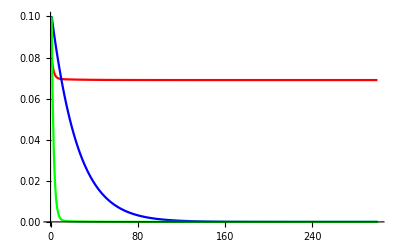

```mathematica
ListLinePlot[Transpose[testrun],PlotStyle->{Red,Blue,Green}]
```

## Vector plots of the dynamics (i.e., plot p2 vs t2 over time when started from different values)

```mathematica
makeRiceFig27[𝓇_,𝓈_,𝒶_,preffunc_,tend_]:=Module[{iter,initPT,out,outT,plotlist},
(* make a list of different starting values at different points in the (p2,t2) grid shown in Fig 2.7 in Rice 2004 *)
initPT=Flatten[Table[{{init,0.01},{init,0.99}},{init,Range[0.05,0.95,0.1]}],1];

(* a list to store figures (I make a fig for each starting value *)
plotlist={};

(* now go through each starting value (p2[i],t2[i]) and iterate the system a certain number of timesteps -- 1000 is enough  *)
For[iter=1,iter≤Length[initPT],iter++,

(* here I iterate that using the function above *)
out=numericallyIterate[𝓇,𝓈,𝒶,preffunc,initPT[[iter]][[1]],initPT[[iter]][[2]],0.1,tend];

(* I only want to store the p2, t2 values for plotting (not the D values) for all timesteps *)
outT=out[[All,{1,2}]];

(* Add the plot to the other list of plots, which we can then all show together using the Show[] command *)
plotlist=Append[plotlist,ListLinePlot[outT,PlotRange->{{0,1},{0,1}}]];
];

(* et voila *)
Show[plotlist]
]
```

```mathematica
finalPlot=makeRiceFig27[0.5,0.7,8,prefFuncKP,1000];
```

General::munfl: 2.51132×10^-136 (-6.68708×10^-173) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.06103×10^-136 (-2.1733×10^-173) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.48285×10^-137 (-7.06323×10^-174) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Line of equilibria:

```mathematica
Solve[(Δt2/.prefFuncKP)==0,t2]
```

{{t2→0},{t2→1},{t2→(p2+s-p2 s-p2 α+p2 s α)/(s (1-α+s α))}}

Superimpose line of equilibria

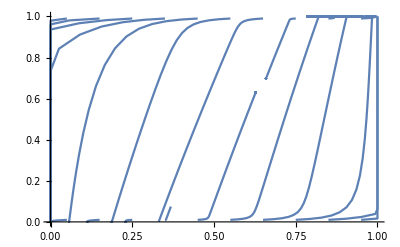

```mathematica
Show[finalPlot]
```

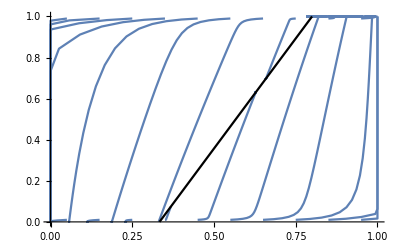

```mathematica
Show[finalPlot,Plot[(p2+s-p2 s-p2 α+p2 s α)/(s (1-α+s α))/.{α->8,s->0.7},{p2,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Black]]
```

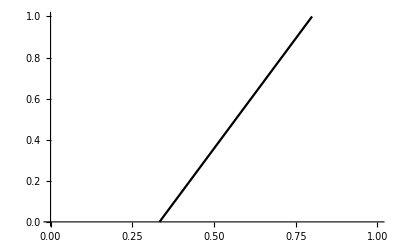

```mathematica
Plot[(p2+s-p2 s-p2 α+p2 s α)/(s (1-α+s α))/.{α->8,s->0.7},{p2,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Black]
```